# Discrete Variational Spherical Pendulum: Free Motion

Brian Beckman
January 2025

## Abstract

We compare three numerical solutions for free motion of an inverted spherical pendulum. Our contribution is to find that only the discrete variational solution exhibits long-term, secular energy conservation at acceptably large time steps. By contrast, numerical integration of the continuous equations of motion exhibits secular energy growth, even at unacceptably small time steps.

The discrete variational approach begins by discretizing dynamical variables and the Lagrangian, replacing continuous functions of time with sequences of discrete quantities. We call this early discretization. Appropriate derivatives of the discrete Lagrangian produce algebraic recurrences that we solve by root-finding. The standard approach delays discretizing continuous functions as late in the process as possible, typically inside opaque solvers for differential equations. We call this late discretization. We find two late-discretized solutions with undesirable secular energy growth. We speculate that all late-discretized solutions will have incorrect secular trends of conserved quantities.

### Details

When dropped from rest at co-latitude, say, 5 degrees, the expected behavior for the pendulum is to swing through the nadir, rise to 355 degrees in the back hemisphere, then fall back around again and repeat. This large-swing motion is convenient for visually checking energy conservation. If the pendulum swings up too far in the back, the solution is gaining energy through secular numerical noise.

Runge-Kutta integration of quaternions at a 1-ms time step immediately gains enough energy to swing all the way through zenith on the first drop. Only by going to 100-μs time step is there even short-term energy conservation. At 100-μs time step, the solution is far slower than real-time, unacceptable for animation.

In pitch/cone-roll coordinates, and with Mathematica’s automatic (and opaque) choices for time step, secular energy conservation is much better, plus we get animation speed. However, there is still secular energy growth. The solution will eventually require rebooting.

By contrast, the early-discretized solution—the discrete variational solution—has no discernable secular energy growth, even at 1-ms time step. There is periodic energy noise in the fourth significant figure, but this is not visible in plots or animations. The periodic noise grows in amplitude, so the solution will eventually require rebooting, but for a different reason. Solution time is much longer than we would like. However, the attractiveness of secular energy conservation warrants further optimization and study of this method.

This notebook is part of a series on discrete variational dynamics. Previous notebooks illustrated harmonic oscillators and the spinning symmetrical top.

## Introduction

Our spherical pendulum is a massive baton of uniform density resting on a massless, sliding, point-like base. The base slides on a ghostly floor: the baton falls through the floor in either direction. When dropped from near upright, the baton falls under its own weight, sliding the base back and then forth. The baton then swings through nadir and back up again via its inertia, sliding the base forth and then back.

In this notebook, we consider only free motion. Later notebooks will address controlling the baton by applying forces to the base.

The spherical pendulum is surprisingly difficult given that the circular pendulum, with one angle and one position coordinate, is an undergraduate exercise with easily solvable optimal control.^[15]  The spherical pendulum is the subject of at least one doctoral thesis.^[7] An internet search for “control inverted spherical pendulum”  produces many references.

For the spherical problem:

Standard spherical coordinates are ruled out because they are singular at the North pole, exactly where we want to balance and control the baton. Control models diverge in these coordinates.

Quaternions have no singularity, but with fourth-order Runge-Kutta (RK4) or Runge-Kutta-Fehlberg (RK45), solutions fail spectacularly, even with 1-ms time step. In this notebook, the integrators are conclusively shown at fault.

Pitch/cone-roll coordinates, developed in this notebook, avoid singularity at the North pole (the control set-point). Continuous equations in these coordinates behave better under late discretization, i.e., standard numerical methods. Numerical solutions in these coordinates have adequate but imperfect secular energy conservation. While small, secular energy growth is a signal that late discretization is fundamentally flawed. Also, while Mathematica’s NDSolve  works well, it does not export out of Mathematica, so we can’t use it for deployed solutions.

Finally, we consider a discrete Lagrangian integrator in pitch/cone-roll coordinates. This has great long-term energy conservation. Its periodic energy noise—in the fourth decimal place—is much larger than the secular-growth noise of the continuous case—in the sixth or seventh decimal place—but still not noticeable visually.

## Outline

late discretization: Integrate continuous Euler-Lagrange equations of motion in quaternions via RK4 and RK45.

Demonstrate fast energy divergence.

late discretization: Integrate continuous Euler-Lagrange equations in pitch/cone-roll coordinates.

Demonstrate slow energy divergence.

early discretization: Develop discrete Euler-Lagrange equations in pitch/cone-roll coordinates. Solve resulting recurrences via root-finding.

Demonstrate secular energy conservation despite periodic noise.

## References

This is a list of general references on discrete variational dynamics and the background mathematics. Not all these references are cited directly in this notebook.

Jack B Kuipers, Quaternions and Rotation Sequences, Princeton University Press, 1999.

Jeongseok Lee, Karen Liu, Frank C. Park, Siddartha S. Srinivasa, A Linear-Time Variational Integrator for Multibody Systems, 2018, https://arxiv.org/abs/1609.02898

Ari Stern, Discrete Geometric Mechanics and Variational Integrators, 2006, http://ddg.cs.columbia.edu/SIGGRAPH06/stern-siggraph-talk.pdf.

Ethan Eade, Lie Groups for 2D and 3D Transformations, 2017, http://ethaneade.com/lie.pdf.

NIST: Digital Library of Mathematical Functions, https://dlmf.nist.gov.

Brian C. Hall, Lie Groups, Lie Algebras, and Representations, Second Edition, 2015, Springer.

Guangyu Liu, Modeling, stabilizing control and trajectory tracking of a spherical inverted pendulum, PhD thesis, 2007, University of Melbourne, 
https://minerva-access.unimelb.edu.au/handle/11343/37225.

Wikipedia, Tennis-Racket Theorem, https://en.wikipedia.org/wiki/Tennis_racket_theorem.

Marin Kobilarov, Keenan Crane, Mathieu Desbrun, Lie Group Integrators for Animation and Control of Vehicles, 2009 (?).

Ari Stern, Mathieu Desbrun, Discrete Geometric Mechanics for Variational Time Integrators, 2006 (http://www.geometry.caltech.edu/pubs/SD06.pdf).

Kenth Engø, On The BCH Formula in 𝔰𝔬(3), https://www.researchgate.net/profile/Kenth_Engo-Monsen2/publication/233591614_On _the _BCH-formula_in _so3/links/004635199177f69467000000/On-the-BCH-formula-in-so3.pdf.

Alexander Van-Brunt, Max Visser, Explicit Baker-Campbell-Hausdorff formulae for some specific Lie algebras, https://arxiv.org/pdf/1505.04505.pdf.

Wikipedia, Baker-Campbell-Hausdorff Formula, https://en.wikipedia.org/wiki/Baker% E2 %80 %93 Campbell % E2 %80 %93 Hausdorff_formula.

Jerrold E. Marsden, Tudor S. Ratiu, Introduction to Mechanics and Symmetry, Second Edition, 2002

Moylan, Andrew, Stabilized Inverted Pendulum, https://blog.wolfram.com/2011/01/19/stabilized-inverted-pendulum/, and Stabilized n-Link Pendulum, https://blog.wolfram.com/2011/03/01/stabilized-n-link-pendulum/

Paul R. Halmos, Naive Set Theory, 2015.

David Lovelock and Hanno Rund, Tensors, Differential Forms, and Variational Principles, 1975.

Ralph Abraham and Jerrold E. Marsden, Foundations of Mechanics: 2nd Edition, 1980.

Taeyoung Lee, Melvin Leok, N. Harris McClamroch, Discrete Control Systems, https://arxiv.org/abs/0705.3868.

Taeyoung Lee, Melvin Leok, N. Harris McClamroch, Global Formulations of Lagrangian and Hamiltonian Mechanics on Manifolds, Springer, https://a.co/d/0lTbL9t.

Tristan Needham, Visual Differential Geometry and Forms, https://a.co/d/9hoKekz.

xAct, Efficient tensor computer algebra for the Wolfram Language, http://xact.es/index.html.

Blanco, Jose-Luis, A tutorial on SE(3) transformation parameterizations and on-manifold optimization, Technical Report #012010, Universidad de Malaga (https://jinyongjeong.github.io/Download/SE3/jlblanco2010geometry3d_techrep.pdf).

Marsden and West has exhaustive treatment of Noether’s Theorem (http://www.cds.caltech.edu/~marsden/bib/2001/09-MaWe2001/MaWe2001.pdf).

Maxime Tournier, Notes on Lie Groups, https://maxime-tournier.github.io/notes/lie-groups.html.

John Baez, Javier P. Muniain, Gauge Fields, Knots and Gravity, (https://a.co/d/jdRnOU0).

F. C. Park, J. E. Bobrow, S. R. Ploen, A Lie Group Formulation of Robot Dynamics.

George W. Hart, Multidimensional Analysis, https://a.co/d/8c5RqOX

Evandro Bernardes, Stephane Viollet, Quaternion to Euler angles conversion: A direct, general and computationally efficient method, PLoS ONE 17(11) e0276302

## Free Rotation Benchmark for TQDL & RK4

This section contains unit tests for TQDL & RK4.

### Show Apparatus

showApparatus is for graphics only, embodying no interesting physics or numerics. Most of the bulk concerns a head’s-up display that requires frequent tweaking. We did not take the effort to properly abstract the head’s-up display.

```mathematica
ClearAll[myFont];
myFont[color_,size_:18]:=Style[#,color,Bold,size,FontFamily->"Courier New"]&;

ClearAll[showApparatus];
showApparatus[t_,ωb_,Lb_,ωs_,Ls_,Ib_,rq_,apparatus_]:=
(Module[{placeZ=1},With[{arrowDiameter=0.02,sq=Sequence@@θvrq[rq],
displaceZ=-0.15},
Show[{
Graphics3D[{
Text[myFont[Blue]["t = "<>ToString[NumberForm[t,{10,2}]]],{-1,-1,placeZ}],

placeZ+=displaceZ;
Text[myFont[Blue][
"|L_s| = "<>ToString[NumberForm[Sqrt[Ls.Ls],{10,4}]]],
{-.975,-1,placeZ}],

placeZ+=displaceZ;
Text[myFont[Blue][
"|L_b| = "<>ToString[NumberForm[Sqrt[Lb.Lb],{10,4}]]],
{-.975,-1,placeZ}],

placeZ+=displaceZ;
Text[myFont[Blue][
"ω_bᵀI_bω_b/2 = "<>ToString[NumberForm[Sqrt[1/2 ωb.Ib.ωb],{10,4}]]],
{-.95,-1,placeZ}],

placeZ+=displaceZ;
Text[myFont[Blue][
"ω_bᵀL_b/2 = "<>ToString[NumberForm[Sqrt[1/2 ωb.Lb],{10,4}]]],
{-.95,-1,placeZ}],

placeZ+=displaceZ;
Text[myFont[Blue][
"ω_sᵀL_s/2 = "<>ToString[NumberForm[Sqrt[1/2 ωs.Ls],{10,4}]]],
{-.95,-1,placeZ}],

Magenta,Arrow[Tube[{o,Ls},arrowDiameter]],
Text[myFont[Black,12]["Inertial-Frame Ang Mom"],{-1.9,+0.2,1},Background->Magenta],

Red,Arrow[Tube[{o,Lb},arrowDiameter]],
Text[myFont[Black,12]["Body-Frame Ang Mom"],{-1.7,-0.1,1},Background->Red],

Cyan,Arrow[Tube[{o,ωs/10},arrowDiameter*1.10]],
Text[myFont[Black,12]["Inertial-Frame Ang Vel"],{-1.4,-0.4,1},Background->Cyan],

Blue,Arrow[Tube[{o,ωb/10},arrowDiameter*1.10]],
Text[myFont[White,12]["Body-Frame Ang Vel"],{-1.3,-0.7,1},Background->Blue],

White,Rotate[apparatus["graphics primitives"],sq]}
]},
Axes->True,
PlotRange->ConstantArray[plotRg,3],
AxesLabel->myFont[Red]/@{"X","Y","Z"},
ImageSize->Large]]]);
```

### Mathematica MomentOfInertia Is Not Moment of Inertia

Beware that Mathematica’s MomentOfInertia built-in returns quantities of fifth degree in the dimension of length. These quantities are actually the product of moment of inertia and volume. The following shows that the ratio of Mathematica’s MomentOfInertia and Mathematica’s Volume for a Cylinder object gives the expected result for the physicist’s moment of inertia. Factors of h and √(h^2) cancel, of course, when h>0, as stipulated. I don’t know why Mathematica won’t cancel them.

```mathematica
With[{body=Cylinder[{{0,0,-h/2},{0,0,h/2}},r]},
With[{ℐ=MomentOfInertia[body,Assumptions->{h>0∧r>0}],𝒱=Volume[body]},
<|"ℐ"->(ℐ//MatrixForm),"𝒱"->𝒱,"ℐ/𝒱"->(ℐ/𝒱//FullSimplify//MatrixForm)|>]]
```

<|ℐ→((π r^2 (h^4+3 h^2 r^2))/(12 √(h^2)) | 0 | 0
0 | (π r^2 (h^4+3 h^2 r^2))/(12 √(h^2)) | 0
0 | 0 | 1/2 √(h^2) π r^4),𝒱→√(h^2) π r^2,ℐ/𝒱→(1/12 (h^2+3 r^2) | 0 | 0
0 | 1/12 (h^2+3 r^2) | 0
0 | 0 | r^2/2)|>

### Run Sim Forced Motion (TQDL & RK4)

Programming  Note—runSimForcedRotationalMotion illustrates an idiom for implicit animation looping via the combination of Dynamic and DynamicModule. Here is a tiny example:

```mathematica
DynamicModule[{t=0,dt=0.03},
Dynamic[t+=dt;t]]
```

```mathematica
ClearAll[oneStepForcedRotationalMotion];
oneStepForcedRotationalMotion[ωb_,rq_,Ib_,Ibi_,dt_,τs_]:=
With[{
ωbNew=ωbn[ωb,Ib,Ibi,dt,τs,rq,rk4],(* changed to rk45 -- no help *)
rqNew=rqb2sn[rq,ωb,dt,rk4]},
With[{LbNew=Ib.ωbNew},
{ωbNew,rqNew,rv[rqNew,ωbNew],LbNew,rv[rqNew,LbNew]}]];

ClearAll[runSimForcedRotationalMotion];
runSimForcedRotationalMotion[
apparatus_,
ωbIn_:{6.,.01,0},
rqIn_:rq[π/4.0,{0, 1., 0}],
fs_:{0,0,0},
τs_:{0,0,0}]:=
With[{ibibi=apparatus["moment of inertia"]},
With[{Ib=ibibi[[1]],Ibi=ibibi[[2]]},
DynamicModule[
{t=0,dt=0.03,ωb=ωbIn,ωs,Lb,Ls,rq=rqIn},
Dynamic[t+=dt;
{ωb,rq,ωs,Lb,Ls}=
oneStepForcedRotationalMotion[ωb,rq,Ib,Ibi,dt,τs];
showApparatus[t,ωb,Lb,ωs,Ls,Ib,rq,apparatus]]]]];
```

## Spherical Pendulum

We now build the graphics and apparatus for the inverted spherical pendulum on a massless cart, and integrate its motion with TQDL & RK4 or RK45.

### Rig (apparatus)

```mathematica
ClearAll[rig];
With[{l=1.2,mass=1.0,d=2.4,r=0.02},
With[{baton=Cylinder[{{0,0,-l},{0,0,+l}},r],
batonCenterBodyFrame={0,0,l}},
(* Immutable constant properties *)
rig["graphics primitives"]=baton;
rig["moment of inertia"]=
With[{Ib=mass*(MomentOfInertia[baton]/Volume[baton])},
With[{Ibi=Inverse@Ib},{Ib,Ibi}]];
rig["cb"]:=batonCenterBodyFrame;
rig["half length"]:=l;
rig["mass"]:=mass;
]];
```

### Axis Jack for Visualizing Orientation

Several overloads

```mathematica
ClearAll[jack];
jack[0,opacity_:0.1,diameter_:0.01]:={
Opacity[opacity],
{Red,Arrow[Tube[{o,e1}],diameter]},
{Darker[Green],Arrow[Tube[{o,e2}],diameter]},
{Blue,Arrow[Tube[{o,e3}],diameter]},
{Lighter[Cyan],Arrow[Tube[{o,-e1}],diameter]},
{Magenta,Arrow[Tube[{o,-e2}],diameter]},
{Yellow,Arrow[Tube[{o,-e3}],diameter]}};
jack[rq_Quaternion,opacity_:0.1,diameter_:0.01]:={
Opacity[opacity],
{Red,Arrow[Tube[{o,rv[rq,e1]}],diameter]},
{Darker[Green],Arrow[Tube[{o,rv[rq,e2]}],diameter]},
{Blue,Arrow[Tube[{o,rv[rq,e3]}],diameter]},
{Lighter[Cyan],Arrow[Tube[{o,rv[rq,-e1]}],diameter]},
{Magenta,Arrow[Tube[{o,rv[rq,-e2]}],diameter]},
{Yellow,Arrow[Tube[{o,rv[rq,-e3]}],diameter]}};
jack[ωHat_List,opacity_:0.1,diameter_:0.01]:={
Opacity[opacity],
{Red,Arrow[Tube[{o,ωHat.e1}],diameter]},
{Darker[Green],Arrow[Tube[{o,ωHat.e2}],diameter]},
{Blue,Arrow[Tube[{o,ωHat.e3}],diameter]},
{Lighter[Cyan],Arrow[Tube[{o,ωHat.-e1}],diameter]},
{Magenta,Arrow[Tube[{o,ωHat.-e2}],diameter]},
{Yellow,Arrow[Tube[{o,ωHat.-e3}],diameter]}};
```

### nfm, vfm, qfm, font: Number-Formatting

nfm For numbers, vfm for vectors, and qfm for quaternions

```mathematica
ClearAll[nfm,vfm,qfm,font];
nfm[num_,dig_:10,dec_:4]:=ToString[NumberForm[Chop@num,{dig,dec}]];
vfm[vec_]:=ToString[NumberForm[#,{7,4},
NumberSigns->{"-"," "}, NumberPadding->{" ", "0"}]&/@Chop@vec];
qfm[q_Quaternion]:=ToString[Map[NumberForm[#,{7,4},
NumberSigns->{"-"," "}, NumberPadding->{" ", "0"}]&,Chop@q,{1}]];
font=myFont[Blue,12];
```

## Discrete Dynamical Integrator

What are good generalized coordinates and velocities? Spherical coordinates have a singularity at the North pole, right where we want to control the baton. A better choice are pitch and cone roll (not axis roll!): co-latitude δ and angular displacement η at a clockwise right angle to the great-circle arc of co-latitude. For any non-zero δ, spinning η makes a non-great circle on the surface around a singularity on the Equator. The demonstration below makes this visually clear. Both δ and η are non-singular at the North pole. η has two singularities on the Equator, when δ is 90° or 270°. But that situation is better than a singularity at the North pole because the baton will fly through these singularities, not linger at them.

The actual physical system is the center of mass of the baton, swinging around the origin. The sliding cart in the animations is a visual fiction. The center of mass of the baton goes up and down.

## Demonstration of the Coordinate System

```mathematica
With[{epsilon=0.0001,h=1/15.,w=1/4.,vu=3.,o={0,0,0},thin={0,0,.0001},cb=rig["cb"]},
With[{kart=Cuboid[{-w,-w,epsilon},{w,w,epsilon+h}],s=2,
floor=Polygon[{{-vu,-vu,0},{vu,-vu,0},{vu,vu,0},{-vu,vu,0}}]},
With[{
c3=Cylinder[{o,thin},s cb[[3]]],b3=Sphere[o,s cb[[3]]],
t3x=Tube[{-s cb[[3]] e2,s cb[[3]] e2},.01],
axisLabelStyle=text↦Style[text,Red,Bold,18,FontFamily->"Courier New"]},
Manipulate[
DynamicModule[{renderPos=o,Στs=o,cs,rotfn},
cs=RotationMatrix[-η,e1].RotationMatrix[δ,e2].cb;
renderPos=-cs[[1]]e1-cs[[2]]e2;
rotfn=RotationTransform[-η,e1]@*RotationTransform[δ,e2];
Show[{
Graphics3D[{
GeometricTransformation[jack[0],rotfn],
{Black,t3x},
(*{White,Opacity[1./2],Cone[{RotationMatrix[δ,e2].cb,o},1]},*)
{White,Opacity[.7/8],c3,b3,
GeometricTransformation[c3,RotationTransform[δ,e2]]},
{Red,Sphere[s cs,1/16.]},
{Yellow,Opacity[.3/4],floor},
{Green,Opacity[.6],Translate[kart,renderPos]},
{White,Opacity[.75],
Translate[
Translate[
GeometricTransformation[rig["graphics primitives"],rotfn],
cs],renderPos+(epsilon+h)e3]}},
ImageSize->Large,Axes->True,AxesLabel->axisLabelStyle/@{"X","Y","Z"},
PlotRange->{{-vu,vu},{-vu,vu},{-vu,vu}}],
ParametricPlot3D[s RotationMatrix[-ha,e1].RotationMatrix[δ,e2].cb,{ha,0,2π}]}]],
{{δ,10°},-360°,360°,1°,Appearance->{"Open"}},
{{η,0°},-360°,360°,1°,Appearance->{"Open"}}]]]]
```

## Dynamical Set-Up

### Center of mass

```mathematica
ClearAll[cm];
(cm[{δ_,η_}]:=RotationMatrix[-η,e1].RotationMatrix[δ,e2].{0,0,Subscript[c, z]});
cm[{δ,η}]//MatrixForm
```

(Sin[δ] c_z
Cos[δ] Sin[η] c_z
Cos[δ] Cos[η] c_z)

### z-Height

The potential energy depends only on the z-height of the CM:

```mathematica
ClearAll[zh];
zh[{δ_,η_}]:=-cm[{δ,η}][[3]];
zh[{δ,η}]
```

-Cos[δ] Cos[η] c_z

### Potential Energy

We’ll need symbolical and numerical functions for energy. The symbolical functions support Mathematica’s calculus with functions like δ[t], η[t], δ '[t], and η'[t]. That calculus yields the equations of motion.^[15] The numerical energy functions support graphics and discrete calculations.

#### numRules

For numerical functions, we replace parametric functions with unbound symbols.

```mathematica
ClearAll[numRules];
numRules={δ[t]->δ,η[t]->η,δ'[t]->Dδ,η'[t]->Dη,m->1,Subscript[c, z]->1.2};
```

```mathematica
ClearAll[Vnum,V];
V[{δ_,η_}]:=m g zh[{δ,η}];V[{δ,η}]
(* Notice not :=, SetDelayed, but =, Set *)
Vnum[{δ_,η_}]=((V[{δ,η}])/.numRules);
Vnum[{δ[t],η[t]}]
```

9.81 m Cos[δ] Cos[η] c_z

11.772 Cos[δ[t]] Cos[η[t]]

### Velocity Vector

The kinetic energy depends on the velocity vector.

```mathematica
ClearAll[v];
(v[{δ_,η_}]:=D[cm[{δ,η}],t]);
v[{δ[t],η[t]}]//FullSimplify//MatrixForm
```

(Cos[δ[t]] c_z δ'[t]
c_z (-Sin[δ[t]] Sin[η[t]] δ'[t]+Cos[δ[t]] Cos[η[t]] η'[t])
-c_z (Cos[η[t]] Sin[δ[t]] δ'[t]+Cos[δ[t]] Sin[η[t]] η'[t]))

### Kinetic Energy

```mathematica
ClearAll[Tnum,T];
(T[{δ_,η_}]:=1/2 m v[{δ,η}].v[{δ,η}]);
T[{δ[t],η[t]}]//FullSimplify
(* hand-constructed, for checking *)
Tnum[{δ_,η_},{Dδ_,Dη_}]:=1/2(1.2)^2(Dδ^2+Cos[δ]^2 Dη^2);
Tnum[{δ_,η_},{Dδ_,Dη_}]:=1/2(1.2)^2(Dδ^2+(1/2(1+Cos[2δ]))Dη^2);
(* Set =, not SetDelayed := *)
Tnum[{δ_,η_},{Dδ_,Dη_}]=(T[{δ[t],η[t]}]/.numRules//FullSimplify);
Tnum[{δ,η},{Dδ,Dη}]
```

1/2 m c_z^2 (δ'[t]^2+Cos[δ[t]]^2 η'[t]^2)

0.72 Dδ^2+0.36 Dη^2+0.36 Dη^2 Cos[2 δ]

### Lagrangians

L is for the late-discretized, standard numerical solution. Lnum  is for the early-discretized Lagrangian, L_d, below.

```mathematica
ClearAll[Lnum,L];
(L[{δ_,η_}]:=T[{δ,η}]-V[{δ,η}]);L[{δ[t],η[t]}]//FullSimplify
Lnum[{δ_,η_},{Dδ_,Dη_}]:=Tnum[{δ,η},{Dδ,Dη}]-Vnum[{δ,η}];
Lnum[{δ,η},{Dδ,Dη}]
```

0.25 m c_z (-39.24 Cos[δ[t]] Cos[η[t]]+c_z (2. δ'[t]^2+(1.+1. Cos[2 δ[t]]) η'[t]^2))

0.72 Dδ^2+0.36 Dη^2+0.36 Dη^2 Cos[2 δ]-11.772 Cos[δ] Cos[η]

### Leqns

Mathematica has symbolical magic for the Euler-Lagrange equations. See Reference [15].

```mathematica
With[{Lcrds={δ[t],η[t]}},
With[{Lvels=D[Lcrds,t]},
With[{Lncnf={0,0}},(* non-conservative forces *)
Leqns=Flatten@MapThread[
{q,v,f}↦D[D[L[Lcrds],v],t]-D[L[Lcrds],q]==f,
{Lcrds,Lvels,Lncnf}]]]]//FullSimplify
```

{m c_z (-9.81 Cos[η[t]] Sin[δ[t]]+c_z (Cos[δ[t]] Sin[δ[t]] η'[t]^2+δ''[t]))==0,m Cos[δ[t]] c_z (-9.81 Sin[η[t]]+c_z (-2. Sin[δ[t]] δ'[t] η'[t]+Cos[δ[t]] η''[t]))==0}

#### State-Space Form

```mathematica
ClearAll[stEqns];
stEqns=Equal@@@(Solve[Leqns,{δ''[t],η''[t]}]//FullSimplify//Chop//Part[#,1]&)
```

{δ''[t]==Sin[δ[t]] ((9.81 Cos[η[t]])/c_z-1. Cos[δ[t]] η'[t]^2),η''[t]==(9.81 Sec[δ[t]] Sin[η[t]])/c_z+2. Tan[δ[t]] δ'[t] η'[t]}

## Late Discretization: Numerical Solution of Continuous Equations

Solve the system for tLim=25 simulated seconds.

```mathematica
ClearAll[tLim,initialConditions,stSolns];
tLim=25;
initialConditions={δ[0]==10°,η[0]==5°,δ'[0]==0,η'[0]==0};
stSolns=NDSolve[Append[stEqns,initialConditions]/.{Subscript[c, z]->1.2},{δ[t],η[t],δ'[t],η'[t]},{t,0,tLim}]
```

{{δ[t]→InterpolatingFunction[…][t],η[t]→InterpolatingFunction[…][t],δ'[t]→InterpolatingFunction[…][t],η'[t]→InterpolatingFunction[…][t]}}

### Plot the Solutions

```mathematica
ClearAll[nsolns];
Manipulate[DynamicModule[{
ics={δ[0]==δ0,η[0]==η0,δ'[0]==0,η'[0]==0},δx,δDotx,ηx,ηDotx,flt},
nsolns=NDSolve[Append[stEqns,ics]/.{Subscript[c, z]->1.2},{δ[t],η[t],δ'[t],η'[t]},{t,0,tL}];
δx=nsolns[[1,1,2]];δDotx=nsolns[[1,3,2]];ηx=nsolns[[1,2,2]];ηDotx=nsolns[[1,4,2]];
flt="δ_0 = "<>ToString[δ0]<>"°, η_0 = "<>ToString[η0]<>"°";
GraphicsGrid[{
{Plot[δx/°,{t,0,tL},FrameLabel->{{"δ [deg]",""},{"t [sec]",flt}},Frame->True],
Plot[δDotx/°,{t,0,tL},FrameLabel->{{"ⅆ_tδ [deg/sec]",""},{"t [sec]",flt}},Frame->True]},
{Plot[ηx/°,{t,0,tL},FrameLabel->{{"η [deg]",""},{"t [sec]",flt}},Frame->True],
Plot[ηDotx/°,{t,0,tL},FrameLabel->{{"ⅆ_tη [deg/sec]",""},{"t [sec]",flt}},Frame->True]}}]],
{{δ0,10.°},0.,90.°},{{η0,5.°},0,90.°},{{tL,25},0,50}]
```

The angles and their derivatives exhibit discontinuities as we saw with quaternions, due merely to choice of branch cuts. The animation below shows smooth motion, plus the pitch angle, here, is visually identical to the pitch-angle plot for the 100-μs quaternion solution.

### Phase Portrait

Plot the angles versus their velocities, proportional to their Hamiltonian conjugate momenta. If the solution were conservative, these phase portraits would be thin lines. When the time constant is long (400 seconds, here), however, they thicken up, showing that the solution is slightly non-conservative, but it’s much better than Runge-Kutta quaternions. This is going to be a good ground-truth.

```mathematica
Manipulate[DynamicModule[{
ics={δ[0]==δ0,η[0]==η0,δ'[0]==0,η'[0]==0},solns,δx,δDotx,ηx,ηDotx},
solns=NDSolve[Append[stEqns,ics]/.{Subscript[c, z]->1.2},{δ[t],η[t],δ'[t],η'[t]},{t,0,tL}];
δx=solns[[1,1,2]];δDotx=solns[[1,3,2]];ηx=solns[[1,2,2]];ηDotx=solns[[1,4,2]];
ParametricPlot[{{δx,δDotx}/°,{ηx,ηDotx}/°},{t,0,tL},PlotLegends->{"δ","η"}]],
{{δ0,10.°},0,90.°},{{η0,5°},0,90.°},{{tL,400},0,500}]
```

### Ground-Truth Animation

This is pretty convincing. Energy is well conserved. We’d only have to reboot it after a long time. If we were satisfied with an integrator that works only inside Mathematica, we’d be just about done. But we want an integrator we can code up in any programming language.

```mathematica
With[{epsilon=0.0001,h=1/15.,w=1/4.,vu=3.},
With[{ztxt=-1.5,xtxt=0,ytxt=-2,znl=0.3},
With[{kart=Cuboid[{-w,-w,epsilon},{w,w,epsilon+h}],
floor=Polygon[{{-vu,-vu,0},{vu,-vu,0},{vu,vu,0},{-vu,vu,0}}],
axisLabelStyle=text↦Style[text,Red,Bold,18,FontFamily->"Courier New"],
cb=rig["cb"],thin={0,0,.0001},s=2,o={0,0,0}},
With[{c3=Cylinder[{o,thin},s cb[[3]]],b3=Sphere[o,s cb[[3]]],t3x=Tube[{-s cb[[3]] e2,s cb[[3]] e2},.01]},
Manipulate[DynamicModule[{
ics={δ[0]==δ0,η[0]==η0,δ'[0]==0,η'[0]==0},solns,δx,Dδx,ηx,Dηx,flt},
solns=NDSolve[Append[stEqns,ics]/.{Subscript[c, z]->1.2},{δ[t],η[t],δ'[t],η'[t]},{t,0,tL}];
δx=solns[[1,1,2]];Dδx=solns[[1,3,2]];ηx=solns[[1,2,2]];Dηx=solns[[1,4,2]];
Animate[
Module[{renderPos=o,cs,rotfn},
cs=RotationMatrix[-ηx/.t->u,e1].RotationMatrix[δx/.t->u,e2].cb;
renderPos=-cs[[1]]e1-cs[[2]]e2;
rotfn=RotationTransform[-ηx/.t->u,e1]@*RotationTransform[δx/.t->u,e2];
Show[{Graphics3D[{
Text[font["t = "<>nfm@u<>
", E = "<>nfm@(Tnum[{δx/.t->u,ηx/.t->u},{Dδx/.t->u,Dηx/.t->u}]+Vnum[{δx/.t->u,ηx/.t->u}])],
{xtxt,ytxt,ztxt}],
Text[font["{δ_0,η_0} = "<>vfm@{δ0/°,η0/°}],{xtxt,ytxt,ztxt-znl}],
Text[font["{δ,η} = "<>vfm@{(δx/.t->u)/°,(ηx/.t->u)/°}],{xtxt,ytxt,ztxt-2znl}],
Text[font["c_s = "<>vfm@cs],{xtxt,ytxt,ztxt-3znl}],
{Black,t3x},
{White,Opacity[.7/8],c3,b3,
GeometricTransformation[c3,RotationTransform[δx/.t->u,e2]]},
GeometricTransformation[jack[0],rotfn],
{Red,Sphere[cs,1/16.]},
{Yellow,Opacity[.3/4],floor},
{Green,Opacity[.6],Translate[kart,renderPos]},
{White,Opacity[.75],Translate[Translate[
GeometricTransformation[rig["graphics primitives"],rotfn],
cs],renderPos+(epsilon+h)e3]}},
ImageSize->Large,Axes->True,AxesLabel->axisLabelStyle/@{"X","Y","Z"},
PlotRange->{{-vu,vu},{-vu,vu},{-vu,vu}}],
ParametricPlot3D[RotationMatrix[-ha,e1].RotationMatrix[δx/.t->u,e2].cb,{ha,0,2π}]}]],
{u,0,tL},AnimationRate->.5]],
{{δ0,10.°},0,90.°},{{η0,5.°},0,90.°},{{tL,25},0,50}]]]]]
```

## Early Discretization

Discretize the dynamical variables and the Lagrangian, itself, via Equation 7 of Reference [10]. First, a reminder:

```mathematica
??Lnum
```

Whereas LNum takes a coordinate tuple q and a velocity tuple q̇, the discrete Lagrangian L_d takes a pair of coordinate tuples: one, q_k, at time t_k, and another, q_(k+1), at time t_(k+1).

L_d is actually discretized action (units of energy × time), being the product of LNum (units of energy) and the finite (constant) time increment dt.

```mathematica
ClearAll[Ld,pk,pkp1,δkm1,ηkm1,δk,ηk,δkp1,ηkp1,dt];
Ld[qk:{δk_,ηk_},qkp1:{δkp1_,ηkp1_},dt_]:=dt Lnum[1/2(qk+qkp1),1/dt(qkp1-qk)];
```

### Discrete Euler-Lagrange Equations

The discrete Euler-Lagrange equations, without generalized force terms, are

D_1 L_d(q_k,q_(k+1))+D_2 L_d(q_(k-1),q_k)=0

```mathematica
ClearAll[d1ld,d2ld];
(* Subscript[D, 1] Subscript[L, d](Subscript[q, k],Subscript[q, k+1]) *)
d1ld[{δk_,ηk_},{δkp1_,ηkp1_},dt_]:=
(* {D[Ld[{δk,ηk},{δkp1,ηkp1},dt],δk]//FullSimplify,
D[Ld[{δk,ηk},{δkp1,ηkp1},dt],ηk]//FullSimplify}, Evaluate in Place *)
{1/dt(-1.44(-δk+δkp1)+5.886 dt^2 Cos[(ηk+ηkp1)/2] Sin[(δk+δkp1)/2]-0.36 (ηk-ηkp1)^2 Sin[δk+δkp1]),
1/dt(0.72ηk-0.72ηkp1+(0.72ηk-0.72ηkp1) Cos[δk+δkp1]+5.886 dt^2 Cos[(δk+δkp1)/2] Sin[(ηk+ηkp1)/2])};
(* +Subscript[D, 2] Subscript[L, d](Subscript[q, k-1],Subscript[q, k]) *)
d2ld[{δkm1_,ηkm1_},{δk_,ηk_},dt_]:=
(* +{D[Ld[{δk,ηk},{δkp1,ηkp1},dt],δkp1]//FullSimplify,
D[Ld[{δk,ηk},{δkp1,ηkp1},dt],ηkp1]//FullSimplify}, Evaluate in Place *){1/dt(1.44 (δk-δkm1)+5.886 dt^2 Cos[(ηk+ηkm1)/2] Sin[(δk+δkm1)/2]-0.36 (ηk-ηkm1)^2 Sin[δk+δkm1]),1/dt(0.72 ηk-0.72 ηkm1+(0.72 ηk-0.72 ηkm1) Cos[δk+δkm1]+5.886 dt^2 Cos[(δk+δkm1)/2] Sin[(ηk+ηkm1)/2])};
```

### Numerical Solution for δ_1 and η_1

All we need is FindRoot, which we could replace with an explicit Newton-Raphson solver in C, C++, Fortran, or Python, for instance. We bootstrap the integrator by taking the first two positions from the late-discretized solution

Notice that the angles are qualitatively the same as for the late-discretized solution.

{7.05693,Null}

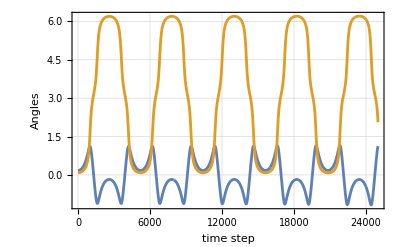

```mathematica
ClearAll[δt,ηt,dt,fh,δ0,η0,δ1,η1,δkm1,ηkm1,δk,ηk,δkp1,ηkp1,tn,len,nvars,dsoln];
δt=nsolns[[1,1,2]];ηt=nsolns[[1,2,2]];
dt=1/1000;(* sec *)fh=1.0*dt;
δ0=δt/.{t->0};η0=ηt/.{t->0};
δ1=δt/.{t->dt};η1=ηt/.{t->dt};
tn= 25; (* sec *)
len=tn/dt;
nvars=2;
dsoln=ConstantArray[0,{2nvars,len}];
dsoln[[1,1]]=δ0;dsoln[[2,1]]=η0;
dsoln[[1,2]]=δ1;dsoln[[2,2]]=η1;
Echo@Quiet@AbsoluteTiming@
For[j=2,j<len,j+=1,
Module[{pj,δkm1,ηkm1,δk,ηk,δkp1,ηkp1,r},
δkm1=dsoln[[1,j-1]];ηkm1=dsoln[[2,j-1]];
δk=dsoln[[1,j]];ηk=dsoln[[2,j]];
pj=d1ld[{δk,ηk},{δkp1,ηkp1},dt]+d2ld[{δkm1,ηkm1},{δk,ηk},dt];
r=FindRoot[pj,{{δkp1,δk},{ηkp1,ηk}}];
dsoln[[1;;2,j+1]]=r[[;;,2]];
dsoln[[3;;4,j+1]]=(dsoln[[1;;2,j+1]]-dsoln[[1;;2,j]])/fh;    ]];
ListLinePlot[dsoln[[1;;2,;;]],Frame->True,GridLines->Automatic,FrameLabel->{{"Angles",""},{"time step",{"Early-Discretized Angles versus Time"}}}]
```

### Energies of the Late Discretization

```mathematica
ClearAll[TnumFlat,VnumFlat];
TnumFlat[δ_,η_,dδ_,dη_]:=Tnum[{δ,η},{dδ,dη}];
VnumFlat[δ_,η_]:=Vnum[{δ,η}];
```

```mathematica
dδ=dsoln[[1]];
dη=dsoln[[2]];
dδDot=dsoln[[3]];
dηDot=dsoln[[4]];
dT=MapThread[TnumFlat,{dδ,dη,dδDot,dηDot}];
dV=MapThread[VnumFlat,{dδ,dη}];
dE=dT+dV;
mdE=Mean[dE];
nδ=Table[nsolns[[1,1,2]]/.t->u,{u,0dt,24999dt,dt}];
nδDot=Table[nsolns[[1,3,2]]/.t->u,{u,0dt,24999dt,dt}];
nη=Table[nsolns[[1,2,2]]/.t->u,{u,0dt,24999dt,dt}];
nηDot=Table[nsolns[[1,4,2]]/.t->u,{u,0dt,24999dt,dt}];
nT=MapThread[TnumFlat,{nδ,nη,nδDot,nηDot}];
nV=MapThread[VnumFlat,{nδ,nη}];
nE=nT+nV;
mnE=Mean[nE];
```

From the late-discretized solution, we calculate an energy of 11.5490. It slowly drifts upward in the fifth decimal place:

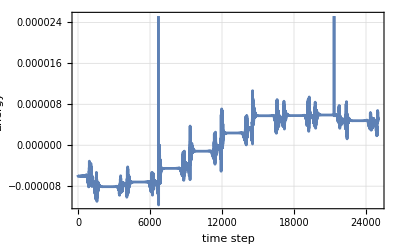

```mathematica
ListLinePlot[nE-mnE, Frame->True,GridLines->Automatic,FrameLabel->{{"Energy",""},{"time step","Late-Discretized Energy versus Time"}}]
```

The late-discretized solution has a mean energy of 11.5486+/-0.014, differing from early-discretized energy in the 5-th figure and with a standard deviation consistent with that difference. The early-discretized solution has a periodic error of about that amplitude, about 2250 times larger than the standard deviation of the energy of the early-discretized solution. However, the big difference is that the late-discretized solution has no discernible secular (linear) trend, whereas the early-discretized solution, when amplified by 2250, has a visually obvious trend.

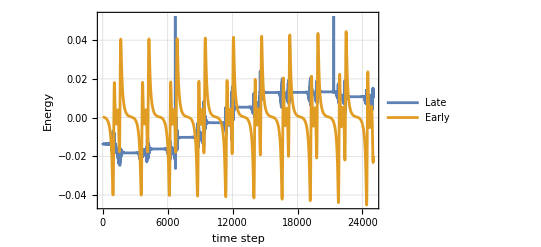

```mathematica
ListLinePlot[{(nE-mnE)*2250,(dE-mdE)},Frame->True,GridLines->Automatic,FrameLabel->{{"Energy", ""},{"time step","Early-Discretized Energy and Late-Discretized Energy versus Time"}},PlotLegends->{"Late","Early"}]
```

## Conclusion

Eventually, the late-discretized solution would accumulate energy, just like the disastrous quaternion-and-Runge-Kutta solution, and would have to be rebooted. We see, again, that early discretization conserves energy much better than late discretization, though with a much larger periodic error. That periodic error is obviously growing in amplitude in the plot, and would eventually require a reboot, too, but for a very different reason.